```mathematica
SetDirectory[NotebookDirectory[]];
```

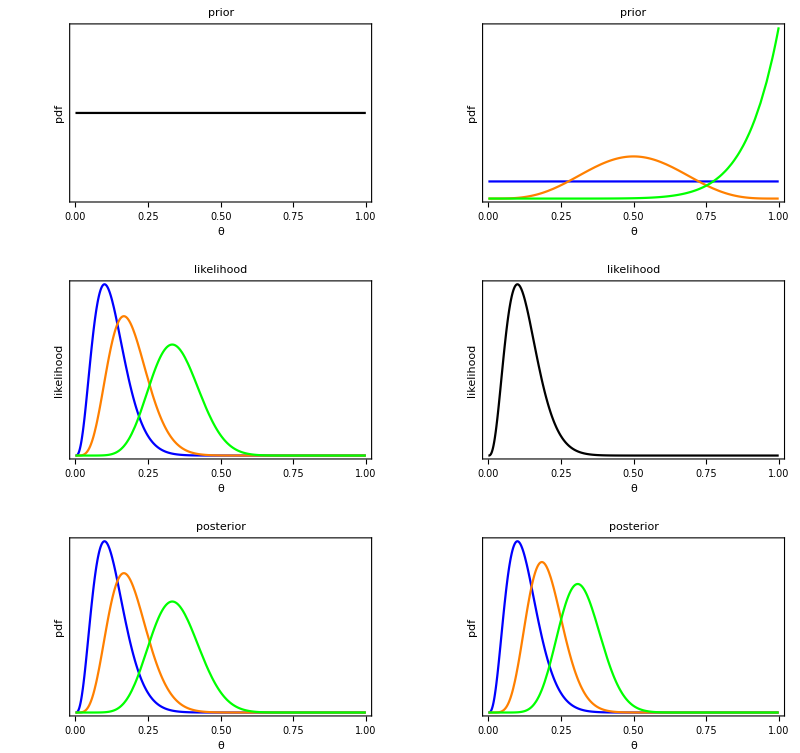

```mathematica
n = 30;
{k1,k2,k3}={3,5,10};
{α,β} = {1,1};
k = 3;
{α1,α2,α3} = {1,5,10};
{β1,β2,β3} = {1,5,1};
gPrior1 = Plot[PDF[BetaDistribution[1,1],x],{x,0,1},Frame->{True,True,False,False},FrameLabel->{"θ","pdf"},PlotStyle->Black,PlotRange->Full,BaseStyle->{FontSize->16},FrameTicks->{True,None},PlotLabel->"prior"];
gLikelihood1 =Plot[{Likelihood[BinomialDistribution[n,θ],{k1}],Likelihood[BinomialDistribution[n,θ],{k2}],Likelihood[BinomialDistribution[n,θ],{k3}]},{θ,0,1},Frame->{True,True,False,False},FrameLabel->{"θ","likelihood "},PlotStyle->{Blue,Orange,Green},PlotRange->Full,BaseStyle->{FontSize->16},FrameTicks->{True,None},PlotLabel->"likelihood"];
gPosterior1 = Plot[{PDF[BetaDistribution[α+k1,β+n-k1],x],PDF[BetaDistribution[α+k2,β+n-k2],x],PDF[BetaDistribution[α+k3,β+n-k3],x]},{x,0,1},Frame->{True,True,False,False},FrameLabel->{"θ","pdf"},PlotStyle->{Blue,Orange,Green},FrameTicks->{True,None},PlotRange->Full,BaseStyle->{FontSize->16},PlotLabel->"posterior"];
gPrior2 = Plot[{PDF[BetaDistribution[α1,β1],x],PDF[BetaDistribution[α2,β2],x],PDF[BetaDistribution[α3,β3],x]},{x,0,1},Frame->{True,True,False,False},FrameLabel->{"θ","pdf"},PlotStyle->{Blue,Orange,Green},PlotRange->Full,BaseStyle->{FontSize->16},FrameTicks->{True,None},PlotLabel->"prior"];
gLikelihood2 =Plot[{Likelihood[BinomialDistribution[n,θ],{k}]},{θ,0,1},Frame->{True,True,False,False},FrameLabel->{"θ","likelihood "},PlotStyle->Black,PlotRange->Full,BaseStyle->{FontSize->16},FrameTicks->{True,None},PlotLabel->"likelihood"];
gPosterior2 = Plot[{PDF[BetaDistribution[α1+k,β1+n-k],x],PDF[BetaDistribution[α2+k,β2+n-k],x],PDF[BetaDistribution[α3+k,β3+n-k],x]},{x,0,1},Frame->{True,True,False,False},FrameLabel->{"θ","pdf"},PlotStyle->{Blue,Orange,Green},FrameTicks->{True,None},PlotRange->Full,BaseStyle->{FontSize->16},PlotLabel->"posterior"];
gFinal=Show[GraphicsGrid[{{gPrior1,gPrior2},{gLikelihood1,gLikelihood2},{gPosterior1,gPosterior2}}],ImageSize->800]
```

```mathematica
Export["Conjugate_binomial.pdf",gFinal]
```

Conjugate_binomial.pdf